# Density of state

```mathematica
(*Equation of motion?*)
M=Flatten[Table[D[Subscript[ρ, n,m][t],t]==-I (Subscript[w, En][n,m])Subscript[ρ, n,m]+I/ℏ Sum[Subscript[d, n,v] Ε[n,v] Subscript[ρ, v,m]-Subscript[ρ, n,v] Subscript[d, v,m] Ε[v,m],{v,1,4}]+If[n≠m,-Subscript[γ, n,m] Subscript[ρ, n,m],Sum[If[n≥ 3,-Γ[v,n] Subscript[ρ, n,n],Γ[n,v] Subscript[ρ, v,v]],{v,1,4}]],{n,1,4},{m,1,4}]//Expand,1];
%//TableForm
```

ρ_(1,1)'[t]==ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]+(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,1) Ε[1,4])/ℏ-(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ-(ⅈ d_(4,1) ρ_(1,4) Ε[4,1])/ℏ-ⅈ ρ_(1,1) w_En[1,1]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)+(ⅈ d_(1,1) ρ_(1,2) Ε[1,1])/ℏ-(ⅈ d_(1,2) ρ_(1,1) Ε[1,2])/ℏ+(ⅈ d_(1,2) ρ_(2,2) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,2) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,2) Ε[1,4])/ℏ-(ⅈ d_(2,2) ρ_(1,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(1,3) Ε[3,2])/ℏ-(ⅈ d_(4,2) ρ_(1,4) Ε[4,2])/ℏ-ⅈ ρ_(1,2) w_En[1,2]
ρ_(1,3)'[t]==-γ_(1,3) ρ_(1,3)+(ⅈ d_(1,1) ρ_(1,3) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,3) Ε[1,2])/ℏ-(ⅈ d_(1,3) ρ_(1,1) Ε[1,3])/ℏ+(ⅈ d_(1,3) ρ_(3,3) Ε[1,3])/ℏ+(ⅈ d_(1,4) ρ_(4,3) Ε[1,4])/ℏ-(ⅈ d_(2,3) ρ_(1,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(1,3) Ε[3,3])/ℏ-(ⅈ d_(4,3) ρ_(1,4) Ε[4,3])/ℏ-ⅈ ρ_(1,3) w_En[1,3]
ρ_(1,4)'[t]==-γ_(1,4) ρ_(1,4)+(ⅈ d_(1,1) ρ_(1,4) Ε[1,1])/ℏ+(ⅈ d_(1,2) ρ_(2,4) Ε[1,2])/ℏ+(ⅈ d_(1,3) ρ_(3,4) Ε[1,3])/ℏ-(ⅈ d_(1,4) ρ_(1,1) Ε[1,4])/ℏ+(ⅈ d_(1,4) ρ_(4,4) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(1,2) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(1,3) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(1,4) Ε[4,4])/ℏ-ⅈ ρ_(1,4) w_En[1,4]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-(ⅈ d_(1,1) ρ_(2,1) Ε[1,1])/ℏ+(ⅈ d_(2,1) ρ_(1,1) Ε[2,1])/ℏ-(ⅈ d_(2,1) ρ_(2,2) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,1) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,1) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,1) Ε[2,4])/ℏ-(ⅈ d_(3,1) ρ_(2,3) Ε[3,1])/ℏ-(ⅈ d_(4,1) ρ_(2,4) Ε[4,1])/ℏ-ⅈ ρ_(2,1) w_En[2,1]
ρ_(2,2)'[t]==ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]-(ⅈ d_(1,2) ρ_(2,1) Ε[1,2])/ℏ+(ⅈ d_(2,1) ρ_(1,2) Ε[2,1])/ℏ+(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,2) Ε[2,4])/ℏ-(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ-(ⅈ d_(4,2) ρ_(2,4) Ε[4,2])/ℏ-ⅈ ρ_(2,2) w_En[2,2]
ρ_(2,3)'[t]==-γ_(2,3) ρ_(2,3)-(ⅈ d_(1,3) ρ_(2,1) Ε[1,3])/ℏ+(ⅈ d_(2,1) ρ_(1,3) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,3) Ε[2,2])/ℏ-(ⅈ d_(2,3) ρ_(2,2) Ε[2,3])/ℏ+(ⅈ d_(2,3) ρ_(3,3) Ε[2,3])/ℏ+(ⅈ d_(2,4) ρ_(4,3) Ε[2,4])/ℏ-(ⅈ d_(3,3) ρ_(2,3) Ε[3,3])/ℏ-(ⅈ d_(4,3) ρ_(2,4) Ε[4,3])/ℏ-ⅈ ρ_(2,3) w_En[2,3]
ρ_(2,4)'[t]==-γ_(2,4) ρ_(2,4)-(ⅈ d_(1,4) ρ_(2,1) Ε[1,4])/ℏ+(ⅈ d_(2,1) ρ_(1,4) Ε[2,1])/ℏ+(ⅈ d_(2,2) ρ_(2,4) Ε[2,2])/ℏ+(ⅈ d_(2,3) ρ_(3,4) Ε[2,3])/ℏ-(ⅈ d_(2,4) ρ_(2,2) Ε[2,4])/ℏ+(ⅈ d_(2,4) ρ_(4,4) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(2,3) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(2,4) Ε[4,4])/ℏ-ⅈ ρ_(2,4) w_En[2,4]
ρ_(3,1)'[t]==-γ_(3,1) ρ_(3,1)-(ⅈ d_(1,1) ρ_(3,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(3,2) Ε[2,1])/ℏ+(ⅈ d_(3,1) ρ_(1,1) Ε[3,1])/ℏ-(ⅈ d_(3,1) ρ_(3,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,1) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,1) Ε[3,3])/ℏ+(ⅈ d_(3,4) ρ_(4,1) Ε[3,4])/ℏ-(ⅈ d_(4,1) ρ_(3,4) Ε[4,1])/ℏ-ⅈ ρ_(3,1) w_En[3,1]
ρ_(3,2)'[t]==-γ_(3,2) ρ_(3,2)-(ⅈ d_(1,2) ρ_(3,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(3,2) Ε[2,2])/ℏ+(ⅈ d_(3,1) ρ_(1,2) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,2) Ε[3,2])/ℏ-(ⅈ d_(3,2) ρ_(3,3) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,2) Ε[3,3])/ℏ+(ⅈ d_(3,4) ρ_(4,2) Ε[3,4])/ℏ-(ⅈ d_(4,2) ρ_(3,4) Ε[4,2])/ℏ-ⅈ ρ_(3,2) w_En[3,2]
ρ_(3,3)'[t]==-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]-(ⅈ d_(1,3) ρ_(3,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(3,2) Ε[2,3])/ℏ+(ⅈ d_(3,1) ρ_(1,3) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,3) Ε[3,2])/ℏ+(ⅈ d_(3,4) ρ_(4,3) Ε[3,4])/ℏ-(ⅈ d_(4,3) ρ_(3,4) Ε[4,3])/ℏ-ⅈ ρ_(3,3) w_En[3,3]
ρ_(3,4)'[t]==-γ_(3,4) ρ_(3,4)-(ⅈ d_(1,4) ρ_(3,1) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(3,2) Ε[2,4])/ℏ+(ⅈ d_(3,1) ρ_(1,4) Ε[3,1])/ℏ+(ⅈ d_(3,2) ρ_(2,4) Ε[3,2])/ℏ+(ⅈ d_(3,3) ρ_(3,4) Ε[3,3])/ℏ-(ⅈ d_(3,4) ρ_(3,3) Ε[3,4])/ℏ+(ⅈ d_(3,4) ρ_(4,4) Ε[3,4])/ℏ-(ⅈ d_(4,4) ρ_(3,4) Ε[4,4])/ℏ-ⅈ ρ_(3,4) w_En[3,4]
ρ_(4,1)'[t]==-γ_(4,1) ρ_(4,1)-(ⅈ d_(1,1) ρ_(4,1) Ε[1,1])/ℏ-(ⅈ d_(2,1) ρ_(4,2) Ε[2,1])/ℏ-(ⅈ d_(3,1) ρ_(4,3) Ε[3,1])/ℏ+(ⅈ d_(4,1) ρ_(1,1) Ε[4,1])/ℏ-(ⅈ d_(4,1) ρ_(4,4) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,1) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,1) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,1) Ε[4,4])/ℏ-ⅈ ρ_(4,1) w_En[4,1]
ρ_(4,2)'[t]==-γ_(4,2) ρ_(4,2)-(ⅈ d_(1,2) ρ_(4,1) Ε[1,2])/ℏ-(ⅈ d_(2,2) ρ_(4,2) Ε[2,2])/ℏ-(ⅈ d_(3,2) ρ_(4,3) Ε[3,2])/ℏ+(ⅈ d_(4,1) ρ_(1,2) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,2) Ε[4,2])/ℏ-(ⅈ d_(4,2) ρ_(4,4) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,2) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,2) Ε[4,4])/ℏ-ⅈ ρ_(4,2) w_En[4,2]
ρ_(4,3)'[t]==-γ_(4,3) ρ_(4,3)-(ⅈ d_(1,3) ρ_(4,1) Ε[1,3])/ℏ-(ⅈ d_(2,3) ρ_(4,2) Ε[2,3])/ℏ-(ⅈ d_(3,3) ρ_(4,3) Ε[3,3])/ℏ+(ⅈ d_(4,1) ρ_(1,3) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,3) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,3) Ε[4,3])/ℏ-(ⅈ d_(4,3) ρ_(4,4) Ε[4,3])/ℏ+(ⅈ d_(4,4) ρ_(4,3) Ε[4,4])/ℏ-ⅈ ρ_(4,3) w_En[4,3]
ρ_(4,4)'[t]==-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]-(ⅈ d_(1,4) ρ_(4,1) Ε[1,4])/ℏ-(ⅈ d_(2,4) ρ_(4,2) Ε[2,4])/ℏ-(ⅈ d_(3,4) ρ_(4,3) Ε[3,4])/ℏ+(ⅈ d_(4,1) ρ_(1,4) Ε[4,1])/ℏ+(ⅈ d_(4,2) ρ_(2,4) Ε[4,2])/ℏ+(ⅈ d_(4,3) ρ_(3,4) Ε[4,3])/ℏ-ⅈ ρ_(4,4) w_En[4,4]

```mathematica
(*Applying Electric field is E Exp[-Iwt]*)
Subscript[w, En][n_,m_]:=If[n>m,w[n,m],-w[m,n]]
Subscript[w, Ex][i_,j_]:=If[i>j,Subscript[w, Ext][i,j],-Subscript[w, Ext][j,i]]
M1=M/.Flatten[Table[ Ε[i,j]->E0[i,j]Exp[-I Subscript[w, Ex][i,j]t],{i,1,4},{j,1,4}]];
%//TableForm
```

ρ_(1,1)'[t]==-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,1))/ℏ+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(1,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(1,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,2))/ℏ+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(1,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(1,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,3))/ℏ+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(1,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(1,4))/ℏ-γ_(1,4) ρ_(1,4)+(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,4))/ℏ+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(2,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(2,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,1))/ℏ-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,2))/ℏ+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(2,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(2,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,3))/ℏ+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(2,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(2,4))/ℏ-γ_(2,4) ρ_(2,4)+(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,4))/ℏ+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(3,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,1))/ℏ-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(3,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,2))/ℏ-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(3,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,4))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,3))/ℏ+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(3,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(3,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(3,4))/ℏ-γ_(3,4) ρ_(3,4)+(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,4))/ℏ+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,1))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(4,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,1))/ℏ-γ_(4,1) ρ_(4,1)-(ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) E0[2,1] d_(2,1) ρ_(4,2))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) E0[3,1] d_(3,1) ρ_(4,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(4,4))/ℏ-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,2))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,1]) E0[1,2] d_(1,2) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(4,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,2))/ℏ-γ_(4,2) ρ_(4,2)-(ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) E0[3,2] d_(3,2) ρ_(4,3))/ℏ-(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(4,4))/ℏ-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,3))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,1]) E0[1,3] d_(1,3) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,2]) E0[2,3] d_(2,3) ρ_(4,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(4,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,3))/ℏ-γ_(4,3) ρ_(4,3)-(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(4,4))/ℏ-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==(ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) E0[4,1] d_(4,1) ρ_(1,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) E0[4,2] d_(4,2) ρ_(2,4))/ℏ+(ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) E0[4,3] d_(4,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,1]) E0[1,4] d_(1,4) ρ_(4,1))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,2]) E0[2,4] d_(2,4) ρ_(4,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,3]) E0[3,4] d_(3,4) ρ_(4,3))/ℏ+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*In terms of rabi frequency*)
M2=M1/.{Subscript[d, 3,1]->(ℏ Ω31)/(2 E0[3,1]),Subscript[d, 1,3]->(ℏ Ω13)/(2 E0[1,3]),Subscript[d, 4,1]->(ℏ Ω41)/(2 E0[4,1]),Subscript[d, 1,4]->(ℏ Ω14)/(2 E0[1,4]),Subscript[d, 3,2]->(ℏ Ω32)/(2 E0[3,2]),Subscript[d, 2,3]->(ℏ Ω23)/(2 E0[2,3]),Subscript[d, 4,2]->(ℏ Ω42)/(2 E0[4,2]),Subscript[d, 2,4]->(ℏ Ω24)/(2 E0[2,4]),Subscript[d, 1,2]->(ℏ Ω12)/(2 E0[1,2]),Subscript[d, 2,1]->(ℏ Ω21)/(2 E0[2,1]),Subscript[d, 3,4]->(ℏ Ω34)/(2 E0[3,4]),Subscript[d, 4,3]->(ℏ Ω43)/(2 E0[4,3])};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,2))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(1,2))/ℏ-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(1,3))/ℏ-γ_(1,3) ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(1,3)+(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(1,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(1,4))/ℏ-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(2,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,1))/ℏ-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,3))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(2,3))/ℏ-γ_(2,3) ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(2,3)+(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(2,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(2,4))/ℏ-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(3,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,1))/ℏ-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,1)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(3,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,2))/ℏ-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,2)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(3,3)+(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(3,4))/ℏ-(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(3,4))/ℏ-γ_(3,4) ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,1)-(ⅈ ⅇ^(ⅈ t w_Ext[1,1]) E0[1,1] d_(1,1) ρ_(4,1))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,1))/ℏ-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(4,1)-(ⅈ ⅇ^(ⅈ t w_Ext[2,2]) E0[2,2] d_(2,2) ρ_(4,2))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,2))/ℏ-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-(ⅈ ⅇ^(ⅈ t w_Ext[3,3]) E0[3,3] d_(3,3) ρ_(4,3))/ℏ+(ⅈ ⅇ^(ⅈ t w_Ext[4,4]) E0[4,4] d_(4,4) ρ_(4,3))/ℏ-γ_(4,3) ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(4,4)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*There is no dipole and w to themselves*)
M3=M2/.{Subscript[d, 1,1]->0,Subscript[d, 2,2]->0,Subscript[d, 3,3]->0,Subscript[d, 4,4]->0,Subscript[w, 1,1]->0,Subscript[w, 2,2]->0,Subscript[w, 3,3]->0,Subscript[w, 4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(1,1)-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(1,3)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,1)-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(2,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(1,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(2,3)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,1)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(3,1)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,2)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(3,3)-γ_(3,4) ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[2,1]) Ω21 ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[2,1]) Ω12 ρ_(4,1)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(4,4)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,3]) Ω43 ρ_(3,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,3]) Ω34 ρ_(4,3)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*Limit 3->4 and 1->2 process*)
M4=M3/.{Ω21 ->0,Ω12 ->0,Ω34 ->0,Ω43 ->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ⅈ ρ_(1,1) w[1,1]+ρ_(1,1) Γ[1,1]+ρ_(2,2) Γ[1,2]+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(2,2) w[2,2]+ρ_(1,1) Γ[2,1]+ρ_(2,2) Γ[2,2]+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+ⅈ ρ_(3,3) w[3,3]-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]-ρ_(3,3) Γ[3,3]-ρ_(3,3) Γ[4,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ⅈ ρ_(4,4) w[4,4]-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]-ρ_(4,4) Γ[3,4]-ρ_(4,4) Γ[4,4]

```mathematica
(*No decay on 3->4 and 1->2, no self decay, no self frequncy*)
M5=M4/.{Γ[2,1]-> 0,Γ[1,2]-> 0,Γ[4,3]-> 0,Γ[3,4]-> 0,Γ[1,1]-> 0,Γ[2,2]-> 0,Γ[3,3]-> 0,Γ[4,4]-> 0,w[1,1]-> 0,w[2,2]->0,w[3,3]->0,w[4,4]->0};
%//TableForm
```

ρ_(1,1)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)+ρ_(3,3) Γ[1,3]+ρ_(4,4) Γ[1,4]
ρ_(1,2)'[t]==-γ_(1,2) ρ_(1,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(1,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,2)+ⅈ ρ_(1,2) w[2,1]
ρ_(1,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(1,2)-γ_(1,3) ρ_(1,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,3)+ⅈ ρ_(1,3) w[3,1]
ρ_(1,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(1,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(1,2)-γ_(1,4) ρ_(1,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,4)+ⅈ ρ_(1,4) w[4,1]
ρ_(2,1)'[t]==-γ_(2,1) ρ_(2,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,1)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,1)-ⅈ ρ_(2,1) w[2,1]
ρ_(2,2)'[t]==-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)+ρ_(3,3) Γ[2,3]+ρ_(4,4) Γ[2,4]
ρ_(2,3)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(2,2)-γ_(2,3) ρ_(2,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,3)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,3)+ⅈ ρ_(2,3) w[3,2]
ρ_(2,4)'[t]==-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(2,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(2,2)-γ_(2,4) ρ_(2,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,4)+1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,4)+ⅈ ρ_(2,4) w[4,2]
ρ_(3,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,1)-γ_(3,1) ρ_(3,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(3,4)-ⅈ ρ_(3,1) w[3,1]
ρ_(3,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,2)-γ_(3,2) ρ_(3,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(3,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(3,4)-ⅈ ρ_(3,2) w[3,2]
ρ_(3,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(3,2)-ρ_(3,3) Γ[1,3]-ρ_(3,3) Γ[2,3]
ρ_(3,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(3,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(3,2)-γ_(3,4) ρ_(3,4)+ⅈ ρ_(3,4) w[4,3]
ρ_(4,1)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,1)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,1)-γ_(4,1) ρ_(4,1)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) Ω31 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(4,4)-ⅈ ρ_(4,1) w[4,1]
ρ_(4,2)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,2)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,2)-γ_(4,2) ρ_(4,2)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) Ω32 ρ_(4,3)-1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(4,4)-ⅈ ρ_(4,2) w[4,2]
ρ_(4,3)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,3)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,3)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,1]) Ω13 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[3,2]) Ω23 ρ_(4,2)-γ_(4,3) ρ_(4,3)-ⅈ ρ_(4,3) w[4,3]
ρ_(4,4)'[t]==1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) Ω41 ρ_(1,4)+1/2 ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) Ω42 ρ_(2,4)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,1]) Ω14 ρ_(4,1)-1/2 ⅈ ⅇ^(ⅈ t w_Ext[4,2]) Ω24 ρ_(4,2)-ρ_(4,4) Γ[1,4]-ρ_(4,4) Γ[2,4]

```mathematica
(*Sending it to Rotating frame!*)
opt={
Subscript[w, Ext][1,1]-> 0,Subscript[w, Ext][2,2]->0,Subscript[w, Ext][3,3]->0,Subscript[w, Ext][4,4]->0,(*no freq itself*)
Subscript[w, Ext][2,1]-> Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2],Subscript[w, Ext][4,3]->Subscript[w, Ext][4,2]-Subscript[w, Ext][3,2](*not allowed transition by other transition field*)
};
rot=Flatten[Table[D[Subscript[ρ, i,j][t],t]-> D[Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],t],{i,1,4},{j,1,4}]/.opt]
rot1=Flatten[Table[Subscript[ρ, i,j]->Subscript[σ, i,j][t]Exp[-I (Subscript[w, Ex][i,j])t],{i,1,4},{j,1,4}]/.opt]
```

{ρ_(1,1)'[t]→σ_(1,1)'[t],ρ_(1,2)'[t]→ⅈ ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(1,2)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)'[t],ρ_(1,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(1,3)[t]+ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)'[t],ρ_(1,4)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[4,1]) w_Ext[4,1] σ_(1,4)[t]+ⅇ^(ⅈ t w_Ext[4,1]) σ_(1,4)'[t],ρ_(2,1)'[t]→-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) (w_Ext[3,1]-w_Ext[3,2]) σ_(2,1)[t]+ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)'[t],ρ_(2,2)'[t]→σ_(2,2)'[t],ρ_(2,3)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(2,3)[t]+ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)'[t],ρ_(2,4)'[t]→ⅈ ⅇ^(ⅈ t w_Ext[4,2]) w_Ext[4,2] σ_(2,4)[t]+ⅇ^(ⅈ t w_Ext[4,2]) σ_(2,4)'[t],ρ_(3,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,1]) w_Ext[3,1] σ_(3,1)[t]+ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)'[t],ρ_(3,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[3,2]) w_Ext[3,2] σ_(3,2)[t]+ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)'[t],ρ_(3,3)'[t]→σ_(3,3)'[t],ρ_(3,4)'[t]→ⅈ ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) (-w_Ext[3,2]+w_Ext[4,2]) σ_(3,4)[t]+ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(3,4)'[t],ρ_(4,1)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[4,1]) w_Ext[4,1] σ_(4,1)[t]+ⅇ^(-ⅈ t w_Ext[4,1]) σ_(4,1)'[t],ρ_(4,2)'[t]→-ⅈ ⅇ^(-ⅈ t w_Ext[4,2]) w_Ext[4,2] σ_(4,2)[t]+ⅇ^(-ⅈ t w_Ext[4,2]) σ_(4,2)'[t],ρ_(4,3)'[t]→-ⅈ ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) (-w_Ext[3,2]+w_Ext[4,2]) σ_(4,3)[t]+ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(4,3)'[t],ρ_(4,4)'[t]→σ_(4,4)'[t]}

{ρ_(1,1)→σ_(1,1)[t],ρ_(1,2)→ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(1,2)[t],ρ_(1,3)→ⅇ^(ⅈ t w_Ext[3,1]) σ_(1,3)[t],ρ_(1,4)→ⅇ^(ⅈ t w_Ext[4,1]) σ_(1,4)[t],ρ_(2,1)→ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2])) σ_(2,1)[t],ρ_(2,2)→σ_(2,2)[t],ρ_(2,3)→ⅇ^(ⅈ t w_Ext[3,2]) σ_(2,3)[t],ρ_(2,4)→ⅇ^(ⅈ t w_Ext[4,2]) σ_(2,4)[t],ρ_(3,1)→ⅇ^(-ⅈ t w_Ext[3,1]) σ_(3,1)[t],ρ_(3,2)→ⅇ^(-ⅈ t w_Ext[3,2]) σ_(3,2)[t],ρ_(3,3)→σ_(3,3)[t],ρ_(3,4)→ⅇ^(ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(3,4)[t],ρ_(4,1)→ⅇ^(-ⅈ t w_Ext[4,1]) σ_(4,1)[t],ρ_(4,2)→ⅇ^(-ⅈ t w_Ext[4,2]) σ_(4,2)[t],ρ_(4,3)→ⅇ^(-ⅈ t (-w_Ext[3,2]+w_Ext[4,2])) σ_(4,3)[t],ρ_(4,4)→σ_(4,4)[t]}

```mathematica
M6=Flatten[Solve[M5/.rot/.rot1,Flatten[Table[Subscript[σ, i,j]'[t],{i,1,4},{j,1,4}]]]//Simplify];
%//TableForm
```

σ_(1,1)'[t]→1/2 (ⅈ (-Ω31 σ_(1,3)[t]-Ω41 σ_(1,4)[t]+Ω13 σ_(3,1)[t]+Ω14 σ_(4,1)[t])+2 (Γ[1,3] σ_(3,3)[t]+Γ[1,4] σ_(4,4)[t]))
σ_(1,2)'[t]→1/2 (-2 γ_(1,2) σ_(1,2)[t]+ⅈ (2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(4,2)[t]))
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→-1/2 ⅈ (Ω14 σ_(1,1)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω24 σ_(1,2)[t]-2 ⅈ γ_(1,4) σ_(1,4)[t]-2 w[4,1] σ_(1,4)[t]+2 w_Ext[4,1] σ_(1,4)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω13 σ_(3,4)[t]-Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→1/2 (-2 γ_(2,1) σ_(2,1)[t]-ⅈ (2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]+Ω31 σ_(2,3)[t]+ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(2,4)[t]-Ω23 σ_(3,1)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω24 σ_(4,1)[t]))
σ_(2,2)'[t]→1/2 (ⅈ (-Ω32 σ_(2,3)[t]-Ω42 σ_(2,4)[t]+Ω23 σ_(3,2)[t]+Ω24 σ_(4,2)[t])+2 (Γ[2,3] σ_(3,3)[t]+Γ[2,4] σ_(4,4)[t]))
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t]-Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→-1/2 ⅈ (ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(2,1)[t]+Ω24 σ_(2,2)[t]-2 ⅈ γ_(2,4) σ_(2,4)[t]-2 w[4,2] σ_(2,4)[t]+2 w_Ext[4,2] σ_(2,4)[t]-Ω23 σ_(3,4)[t]-Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-ⅇ^(ⅈ t (-w_Ext[3,1]+w_Ext[3,2]+w_Ext[4,1]-w_Ext[4,2])) Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t]+2 w[4,3] σ_(3,4)[t]+2 w_Ext[3,2] σ_(3,4)[t]-2 w_Ext[4,2] σ_(3,4)[t])
σ_(4,1)'[t]→1/2 (ⅈ Ω41 σ_(1,1)[t]+ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω42 σ_(2,1)[t]-2 γ_(4,1) σ_(4,1)[t]-2 ⅈ w[4,1] σ_(4,1)[t]+2 ⅈ w_Ext[4,1] σ_(4,1)[t]-ⅈ ⅇ^(-ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω31 σ_(4,3)[t]-ⅈ Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-2 w[4,2] σ_(4,2)[t]+2 w_Ext[4,2] σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-ⅇ^(ⅈ t (w_Ext[3,1]-w_Ext[3,2]-w_Ext[4,1]+w_Ext[4,2])) Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t]-2 w[4,3] σ_(4,3)[t]-2 w_Ext[3,2] σ_(4,3)[t]+2 w_Ext[4,2] σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Some frequncy algebra*)
M7=M6/.{ⅇ^(ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2]))->1,ⅇ^(ⅈ t (-Subscript[w, Ext][3,1]+Subscript[w, Ext][3,2]+Subscript[w, Ext][4,1]-Subscript[w, Ext][4,2]))->1,(ⅇ^(-ⅈ t (Subscript[w, Ext][3,1]-Subscript[w, Ext][3,2]-Subscript[w, Ext][4,1]+Subscript[w, Ext][4,2])))->1}//Simplify;
%//TableForm
```

σ_(1,1)'[t]→1/2 (ⅈ (-Ω31 σ_(1,3)[t]-Ω41 σ_(1,4)[t]+Ω13 σ_(3,1)[t]+Ω14 σ_(4,1)[t])+2 (Γ[1,3] σ_(3,3)[t]+Γ[1,4] σ_(4,4)[t]))
σ_(1,2)'[t]→1/2 ⅈ (2 ⅈ γ_(1,2) σ_(1,2)[t]+2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+Ω14 σ_(4,2)[t])
σ_(1,3)'[t]→-1/2 ⅈ (Ω13 σ_(1,1)[t]+Ω23 σ_(1,2)[t]-2 ⅈ γ_(1,3) σ_(1,3)[t]-2 w[3,1] σ_(1,3)[t]+2 w_Ext[3,1] σ_(1,3)[t]-Ω13 σ_(3,3)[t]-Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→1/2 ⅈ (-Ω14 σ_(1,1)[t]-Ω24 σ_(1,2)[t]+2 ⅈ γ_(1,4) σ_(1,4)[t]+2 w[4,1] σ_(1,4)[t]-2 w_Ext[4,1] σ_(1,4)[t]+Ω13 σ_(3,4)[t]+Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→1/2 ⅈ (2 ⅈ γ_(2,1) σ_(2,1)[t]-2 (w[2,1]-w_Ext[3,1]+w_Ext[3,2]) σ_(2,1)[t]-Ω31 σ_(2,3)[t]-Ω41 σ_(2,4)[t]+Ω23 σ_(3,1)[t]+Ω24 σ_(4,1)[t])
σ_(2,2)'[t]→1/2 (ⅈ (-Ω32 σ_(2,3)[t]-Ω42 σ_(2,4)[t]+Ω23 σ_(3,2)[t]+Ω24 σ_(4,2)[t])+2 (Γ[2,3] σ_(3,3)[t]+Γ[2,4] σ_(4,4)[t]))
σ_(2,3)'[t]→-1/2 ⅈ (Ω13 σ_(2,1)[t]+Ω23 σ_(2,2)[t]-2 ⅈ γ_(2,3) σ_(2,3)[t]-2 w[3,2] σ_(2,3)[t]+2 w_Ext[3,2] σ_(2,3)[t]-Ω23 σ_(3,3)[t]-Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→-1/2 ⅈ (Ω14 σ_(2,1)[t]+Ω24 σ_(2,2)[t]-2 ⅈ γ_(2,4) σ_(2,4)[t]-2 w[4,2] σ_(2,4)[t]+2 w_Ext[4,2] σ_(2,4)[t]-Ω23 σ_(3,4)[t]-Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-2 w[3,1] σ_(3,1)[t]+2 w_Ext[3,1] σ_(3,1)[t]-Ω31 σ_(3,3)[t]-Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-2 w[3,2] σ_(3,2)[t]+2 w_Ext[3,2] σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t]+2 w[4,3] σ_(3,4)[t]+2 w_Ext[3,2] σ_(3,4)[t]-2 w_Ext[4,2] σ_(3,4)[t])
σ_(4,1)'[t]→1/2 ⅈ (Ω41 σ_(1,1)[t]+Ω42 σ_(2,1)[t]+2 ⅈ γ_(4,1) σ_(4,1)[t]-2 w[4,1] σ_(4,1)[t]+2 w_Ext[4,1] σ_(4,1)[t]-Ω31 σ_(4,3)[t]-Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-2 w[4,2] σ_(4,2)[t]+2 w_Ext[4,2] σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t]-2 w[4,3] σ_(4,3)[t]-2 w_Ext[3,2] σ_(4,3)[t]+2 w_Ext[4,2] σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Let's Look at the difference of the frequncy*)
twophoton={w[2,1]-> Subscript[w, Ext][3,1]+Δ1-Subscript[w, Ext][3,2]-Δ3, w[4,3] ->-  Subscript[w, Ext][3,2] -Δ3+ Subscript[w, Ext][4,2]+Δ4};
onephoton={ w[3,1]->  Subscript[w, Ext][3,1]+Δ1,w[4,1] ->  Subscript[w, Ext][4,1]+Δ2,w[3,2]->  Subscript[w, Ext][3,2]+Δ3 , w[4,2] ->  Subscript[w, Ext][4,2] +Δ4};
M8=Simplify[Expand[M7/.twophoton/.onephoton]];
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω41 σ_(1,4)[t]-Ω13 σ_(3,1)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]-Ω14 σ_(4,1)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t])
σ_(1,2)'[t]→1/2 ⅈ (2 (Δ1-Δ3+ⅈ γ_(1,2)) σ_(1,2)[t]-Ω32 σ_(1,3)[t]-Ω42 σ_(1,4)[t]+Ω13 σ_(3,2)[t]+Ω14 σ_(4,2)[t])
σ_(1,3)'[t]→1/2 ⅈ (-Ω13 σ_(1,1)[t]-Ω23 σ_(1,2)[t]+2 Δ1 σ_(1,3)[t]+2 ⅈ γ_(1,3) σ_(1,3)[t]+Ω13 σ_(3,3)[t]+Ω14 σ_(4,3)[t])
σ_(1,4)'[t]→1/2 ⅈ (-Ω14 σ_(1,1)[t]-Ω24 σ_(1,2)[t]+2 Δ2 σ_(1,4)[t]+2 ⅈ γ_(1,4) σ_(1,4)[t]+Ω13 σ_(3,4)[t]+Ω14 σ_(4,4)[t])
σ_(2,1)'[t]→-1/2 ⅈ (2 (Δ1-Δ3-ⅈ γ_(2,1)) σ_(2,1)[t]+Ω31 σ_(2,3)[t]+Ω41 σ_(2,4)[t]-Ω23 σ_(3,1)[t]-Ω24 σ_(4,1)[t])
σ_(2,2)'[t]→-1/2 ⅈ (Ω32 σ_(2,3)[t]+Ω42 σ_(2,4)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])
σ_(2,3)'[t]→1/2 ⅈ (-Ω13 σ_(2,1)[t]-Ω23 σ_(2,2)[t]+2 Δ3 σ_(2,3)[t]+2 ⅈ γ_(2,3) σ_(2,3)[t]+Ω23 σ_(3,3)[t]+Ω24 σ_(4,3)[t])
σ_(2,4)'[t]→1/2 ⅈ (-Ω14 σ_(2,1)[t]-Ω24 σ_(2,2)[t]+2 Δ4 σ_(2,4)[t]+2 ⅈ γ_(2,4) σ_(2,4)[t]+Ω23 σ_(3,4)[t]+Ω24 σ_(4,4)[t])
σ_(3,1)'[t]→1/2 ⅈ (Ω31 σ_(1,1)[t]+Ω32 σ_(2,1)[t]-2 Δ1 σ_(3,1)[t]+2 ⅈ γ_(3,1) σ_(3,1)[t]-Ω31 σ_(3,3)[t]-Ω41 σ_(3,4)[t])
σ_(3,2)'[t]→1/2 ⅈ (Ω31 σ_(1,2)[t]+Ω32 σ_(2,2)[t]-2 Δ3 σ_(3,2)[t]+2 ⅈ γ_(3,2) σ_(3,2)[t]-Ω32 σ_(3,3)[t]-Ω42 σ_(3,4)[t])
σ_(3,3)'[t]→1/2 ⅈ (Ω31 σ_(1,3)[t]+Ω32 σ_(2,3)[t]-Ω13 σ_(3,1)[t]-Ω23 σ_(3,2)[t]+2 ⅈ Γ[1,3] σ_(3,3)[t]+2 ⅈ Γ[2,3] σ_(3,3)[t])
σ_(3,4)'[t]→1/2 ⅈ (Ω31 σ_(1,4)[t]+Ω32 σ_(2,4)[t]-Ω14 σ_(3,1)[t]-Ω24 σ_(3,2)[t]-2 Δ3 σ_(3,4)[t]+2 Δ4 σ_(3,4)[t]+2 ⅈ γ_(3,4) σ_(3,4)[t])
σ_(4,1)'[t]→1/2 ⅈ (Ω41 σ_(1,1)[t]+Ω42 σ_(2,1)[t]-2 Δ2 σ_(4,1)[t]+2 ⅈ γ_(4,1) σ_(4,1)[t]-Ω31 σ_(4,3)[t]-Ω41 σ_(4,4)[t])
σ_(4,2)'[t]→1/2 ⅈ (Ω41 σ_(1,2)[t]+Ω42 σ_(2,2)[t]-2 Δ4 σ_(4,2)[t]+2 ⅈ γ_(4,2) σ_(4,2)[t]-Ω32 σ_(4,3)[t]-Ω42 σ_(4,4)[t])
σ_(4,3)'[t]→1/2 ⅈ (Ω41 σ_(1,3)[t]+Ω42 σ_(2,3)[t]-Ω13 σ_(4,1)[t]-Ω23 σ_(4,2)[t]+2 Δ3 σ_(4,3)[t]-2 Δ4 σ_(4,3)[t]+2 ⅈ γ_(4,3) σ_(4,3)[t])
σ_(4,4)'[t]→1/2 ⅈ (Ω41 σ_(1,4)[t]+Ω42 σ_(2,4)[t]-Ω14 σ_(4,1)[t]-Ω24 σ_(4,2)[t]+2 ⅈ Γ[1,4] σ_(4,4)[t]+2 ⅈ Γ[2,4] σ_(4,4)[t])

```mathematica
(*Now make this into two field*)
opt1={Δ2-> w43+Δ1,Δ4-> w43+Δ3,Ω41->Sqrt[7/2]Ω31,Ω14->Sqrt[7/2]Ω13,Ω42->Sqrt[4/5]Ω32,Ω24->Sqrt[4/5]Ω23};
(*Two Photon detuning*)
opt2={Δ3-> δ+Δ1};
M9=M8/.opt1/.opt2//Expand;
%//TableForm
```

σ_(1,1)'[t]→-1/2 ⅈ Ω31 σ_(1,3)[t]-1/2 ⅈ √(7/2) Ω31 σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,1)[t]+Γ[1,3] σ_(3,3)[t]+1/2 ⅈ √(7/2) Ω13 σ_(4,1)[t]+Γ[1,4] σ_(4,4)[t]
σ_(1,2)'[t]→-ⅈ δ σ_(1,2)[t]-γ_(1,2) σ_(1,2)[t]-1/2 ⅈ Ω32 σ_(1,3)[t]-(ⅈ Ω32 σ_(1,4)[t])/(√5)+1/2 ⅈ Ω13 σ_(3,2)[t]+1/2 ⅈ √(7/2) Ω13 σ_(4,2)[t]
σ_(1,3)'[t]→-1/2 ⅈ Ω13 σ_(1,1)[t]-1/2 ⅈ Ω23 σ_(1,2)[t]+ⅈ Δ1 σ_(1,3)[t]-γ_(1,3) σ_(1,3)[t]+1/2 ⅈ Ω13 σ_(3,3)[t]+1/2 ⅈ √(7/2) Ω13 σ_(4,3)[t]
σ_(1,4)'[t]→-1/2 ⅈ √(7/2) Ω13 σ_(1,1)[t]-(ⅈ Ω23 σ_(1,2)[t])/(√5)+ⅈ w43 σ_(1,4)[t]+ⅈ Δ1 σ_(1,4)[t]-γ_(1,4) σ_(1,4)[t]+1/2 ⅈ Ω13 σ_(3,4)[t]+1/2 ⅈ √(7/2) Ω13 σ_(4,4)[t]
σ_(2,1)'[t]→ⅈ δ σ_(2,1)[t]-γ_(2,1) σ_(2,1)[t]-1/2 ⅈ Ω31 σ_(2,3)[t]-1/2 ⅈ √(7/2) Ω31 σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,1)[t]+(ⅈ Ω23 σ_(4,1)[t])/(√5)
σ_(2,2)'[t]→-1/2 ⅈ Ω32 σ_(2,3)[t]-(ⅈ Ω32 σ_(2,4)[t])/(√5)+1/2 ⅈ Ω23 σ_(3,2)[t]+Γ[2,3] σ_(3,3)[t]+(ⅈ Ω23 σ_(4,2)[t])/(√5)+Γ[2,4] σ_(4,4)[t]
σ_(2,3)'[t]→-1/2 ⅈ Ω13 σ_(2,1)[t]-1/2 ⅈ Ω23 σ_(2,2)[t]+ⅈ δ σ_(2,3)[t]+ⅈ Δ1 σ_(2,3)[t]-γ_(2,3) σ_(2,3)[t]+1/2 ⅈ Ω23 σ_(3,3)[t]+(ⅈ Ω23 σ_(4,3)[t])/(√5)
σ_(2,4)'[t]→-1/2 ⅈ √(7/2) Ω13 σ_(2,1)[t]-(ⅈ Ω23 σ_(2,2)[t])/(√5)+ⅈ w43 σ_(2,4)[t]+ⅈ δ σ_(2,4)[t]+ⅈ Δ1 σ_(2,4)[t]-γ_(2,4) σ_(2,4)[t]+1/2 ⅈ Ω23 σ_(3,4)[t]+(ⅈ Ω23 σ_(4,4)[t])/(√5)
σ_(3,1)'[t]→1/2 ⅈ Ω31 σ_(1,1)[t]+1/2 ⅈ Ω32 σ_(2,1)[t]-ⅈ Δ1 σ_(3,1)[t]-γ_(3,1) σ_(3,1)[t]-1/2 ⅈ Ω31 σ_(3,3)[t]-1/2 ⅈ √(7/2) Ω31 σ_(3,4)[t]
σ_(3,2)'[t]→1/2 ⅈ Ω31 σ_(1,2)[t]+1/2 ⅈ Ω32 σ_(2,2)[t]-ⅈ δ σ_(3,2)[t]-ⅈ Δ1 σ_(3,2)[t]-γ_(3,2) σ_(3,2)[t]-1/2 ⅈ Ω32 σ_(3,3)[t]-(ⅈ Ω32 σ_(3,4)[t])/(√5)
σ_(3,3)'[t]→1/2 ⅈ Ω31 σ_(1,3)[t]+1/2 ⅈ Ω32 σ_(2,3)[t]-1/2 ⅈ Ω13 σ_(3,1)[t]-1/2 ⅈ Ω23 σ_(3,2)[t]-Γ[1,3] σ_(3,3)[t]-Γ[2,3] σ_(3,3)[t]
σ_(3,4)'[t]→1/2 ⅈ Ω31 σ_(1,4)[t]+1/2 ⅈ Ω32 σ_(2,4)[t]-1/2 ⅈ √(7/2) Ω13 σ_(3,1)[t]-(ⅈ Ω23 σ_(3,2)[t])/(√5)+ⅈ w43 σ_(3,4)[t]-γ_(3,4) σ_(3,4)[t]
σ_(4,1)'[t]→1/2 ⅈ √(7/2) Ω31 σ_(1,1)[t]+(ⅈ Ω32 σ_(2,1)[t])/(√5)-ⅈ w43 σ_(4,1)[t]-ⅈ Δ1 σ_(4,1)[t]-γ_(4,1) σ_(4,1)[t]-1/2 ⅈ Ω31 σ_(4,3)[t]-1/2 ⅈ √(7/2) Ω31 σ_(4,4)[t]
σ_(4,2)'[t]→1/2 ⅈ √(7/2) Ω31 σ_(1,2)[t]+(ⅈ Ω32 σ_(2,2)[t])/(√5)-ⅈ w43 σ_(4,2)[t]-ⅈ δ σ_(4,2)[t]-ⅈ Δ1 σ_(4,2)[t]-γ_(4,2) σ_(4,2)[t]-1/2 ⅈ Ω32 σ_(4,3)[t]-(ⅈ Ω32 σ_(4,4)[t])/(√5)
σ_(4,3)'[t]→1/2 ⅈ √(7/2) Ω31 σ_(1,3)[t]+(ⅈ Ω32 σ_(2,3)[t])/(√5)-1/2 ⅈ Ω13 σ_(4,1)[t]-1/2 ⅈ Ω23 σ_(4,2)[t]-ⅈ w43 σ_(4,3)[t]-γ_(4,3) σ_(4,3)[t]
σ_(4,4)'[t]→1/2 ⅈ √(7/2) Ω31 σ_(1,4)[t]+(ⅈ Ω32 σ_(2,4)[t])/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(4,1)[t]-(ⅈ Ω23 σ_(4,2)[t])/(√5)-Γ[1,4] σ_(4,4)[t]-Γ[2,4] σ_(4,4)[t]

```mathematica
(*Steady State Solution*)
M10=Table[(M9[[All,2]]/.Flatten[Table[{Subscript[σ, i,j][t]->Subscript[σ, i,j],Subscript[γ, i,j]->ToExpression["γ"<>ToString[i]<>ToString[j]],Γ[i,j]->ToExpression["Γ"<>ToString[i]<>ToString[j]]},{i,1,4},{j,1,4}]])[[i]]==0,{i,1,16}];
%//TableForm
```

-1/2 ⅈ Ω31 σ_(1,3)-1/2 ⅈ √(7/2) Ω31 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,1)+Γ13 σ_(3,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,1)+Γ14 σ_(4,4)==0
-γ12 σ_(1,2)-ⅈ δ σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-(ⅈ Ω32 σ_(1,4))/(√5)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ √(7/2) Ω13 σ_(4,2)==0
-1/2 ⅈ Ω13 σ_(1,1)-1/2 ⅈ Ω23 σ_(1,2)-γ13 σ_(1,3)+ⅈ Δ1 σ_(1,3)+1/2 ⅈ Ω13 σ_(3,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,3)==0
-1/2 ⅈ √(7/2) Ω13 σ_(1,1)-(ⅈ Ω23 σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)-γ14 σ_(1,4)+ⅈ Δ1 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)+1/2 ⅈ √(7/2) Ω13 σ_(4,4)==0
-γ21 σ_(2,1)+ⅈ δ σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ √(7/2) Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+(ⅈ Ω23 σ_(4,1))/(√5)==0
-1/2 ⅈ Ω32 σ_(2,3)-(ⅈ Ω32 σ_(2,4))/(√5)+1/2 ⅈ Ω23 σ_(3,2)+Γ23 σ_(3,3)+(ⅈ Ω23 σ_(4,2))/(√5)+Γ24 σ_(4,4)==0
-1/2 ⅈ Ω13 σ_(2,1)-1/2 ⅈ Ω23 σ_(2,2)-γ23 σ_(2,3)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)+1/2 ⅈ Ω23 σ_(3,3)+(ⅈ Ω23 σ_(4,3))/(√5)==0
-1/2 ⅈ √(7/2) Ω13 σ_(2,1)-(ⅈ Ω23 σ_(2,2))/(√5)+ⅈ w43 σ_(2,4)-γ24 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)+(ⅈ Ω23 σ_(4,4))/(√5)==0
1/2 ⅈ Ω31 σ_(1,1)+1/2 ⅈ Ω32 σ_(2,1)-γ31 σ_(3,1)-ⅈ Δ1 σ_(3,1)-1/2 ⅈ Ω31 σ_(3,3)-1/2 ⅈ √(7/2) Ω31 σ_(3,4)==0
1/2 ⅈ Ω31 σ_(1,2)+1/2 ⅈ Ω32 σ_(2,2)-γ32 σ_(3,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-1/2 ⅈ Ω32 σ_(3,3)-(ⅈ Ω32 σ_(3,4))/(√5)==0
1/2 ⅈ Ω31 σ_(1,3)+1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(3,1)-1/2 ⅈ Ω23 σ_(3,2)-Γ13 σ_(3,3)-Γ23 σ_(3,3)==0
1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ √(7/2) Ω13 σ_(3,1)-(ⅈ Ω23 σ_(3,2))/(√5)+ⅈ w43 σ_(3,4)-γ34 σ_(3,4)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,1)+(ⅈ Ω32 σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)-γ41 σ_(4,1)-ⅈ Δ1 σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)-1/2 ⅈ √(7/2) Ω31 σ_(4,4)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,2)+(ⅈ Ω32 σ_(2,2))/(√5)-ⅈ w43 σ_(4,2)-γ42 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)-(ⅈ Ω32 σ_(4,4))/(√5)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,3)+(ⅈ Ω32 σ_(2,3))/(√5)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-γ43 σ_(4,3)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,4)+(ⅈ Ω32 σ_(2,4))/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(4,1)-(ⅈ Ω23 σ_(4,2))/(√5)-Γ14 σ_(4,4)-Γ24 σ_(4,4)==0

# Difference Power(Prob Diam=0.5mm, Couple 1mm)

```mathematica
ℏ=1.0546 10^-34;e0=8.8542 10^-12;c=2.9979 10^8;diam=1/1000;d32=Sqrt[5/27]*2.537717 10^-29;diam2=0.5/1000;
Subscript[γ, 3,1]=2*Pi*5.750056 10^6/2;Subscript[γ, 1,3]=2*Pi*5.750056 10^6/2;Subscript[γ, 3,2]=2*Pi*5.750056 10^6/2;Subscript[γ, 2,3]=2*Pi*5.750056 10^6/2;Subscript[γ, 4,1]=2*Pi*5.750056 10^6/2;
Subscript[γ, 1,4]=2*Pi*5.750056 10^6/2;Subscript[γ, 4,2]=2*Pi*5.750056 10^6/2;Subscript[γ, 2,4]=2*Pi*5.750056 10^6/2;w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;Subscript[γ, 1,2]=2Pi 1.4*10^6;
Subscript[γ, 2,1]=2Pi 1.4*10^6;Subscript[γ, 4,3]=2*Pi*5.750056 10^6;Subscript[γ, 3,4]=2*Pi*5.750056 10^6;
```

## Power=0.1mW

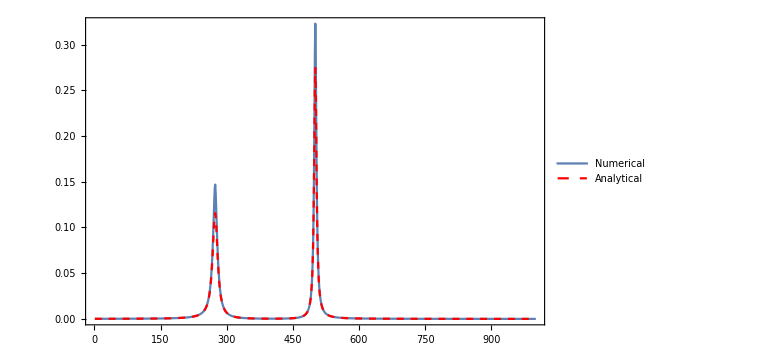

```mathematica
P1=0.1/1000;
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLegends-> {"Numerical"},Frame->True,Axes->False,ImageSize->Large
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends-> {"Analytical"}];
Show[a1,a2]
```

## Power=1mW

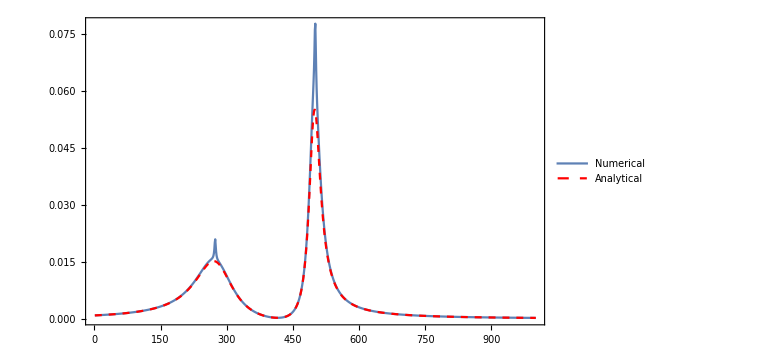

```mathematica
P1=1/1000;
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLegends-> {"Numerical"},Frame->True,Axes->False,ImageSize->Large
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends-> {"Analytical"}];
Show[a1,a2]
```

## Power=10mW

```mathematica
Ω13
Ω23
```

2.26793×10^8

1.79296×10^7

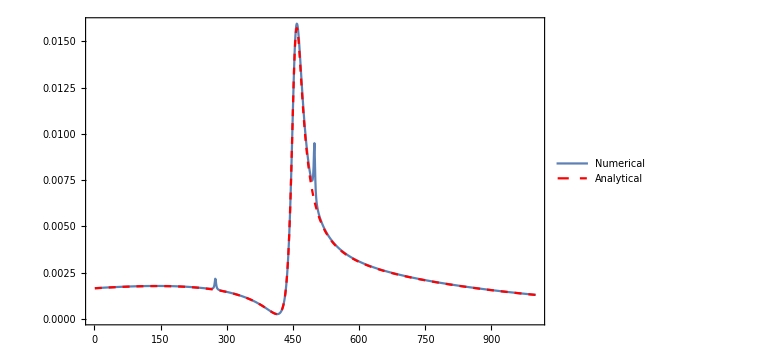

```mathematica
P1=10/1000;
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLegends-> {"Numerical"},Frame->True,Axes->False,ImageSize->Large
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends-> {"Analytical"}];
Show[a1,a2]
```

## Power=100mW

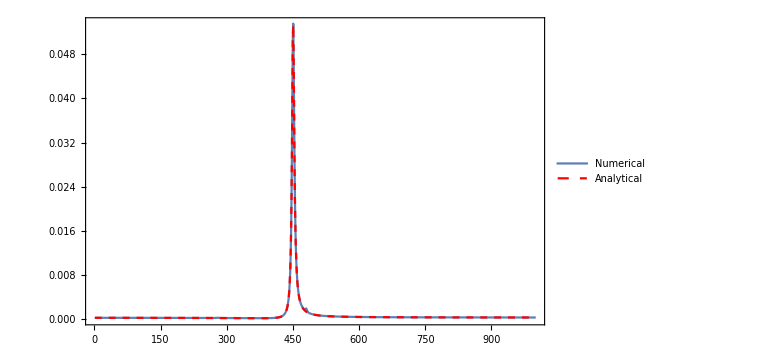

```mathematica
P1=100/1000;
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLegends-> {"Numerical"},Frame->True,Axes->False,ImageSize->Large
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends-> {"Analytical"}];
Show[a1,a2]
```

## Power=1000mW

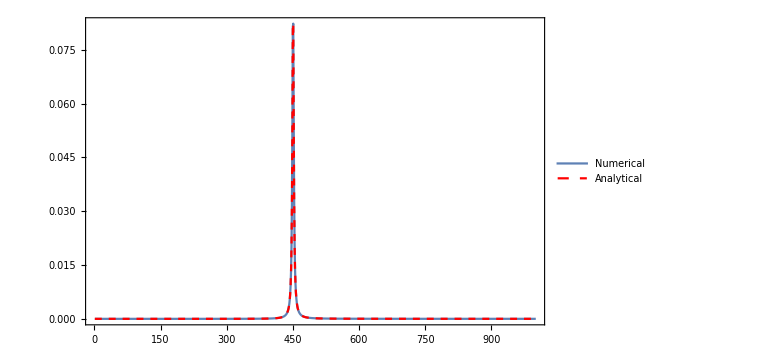

```mathematica
P1=1000/1000;
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLegends-> {"Numerical"},Frame->True,Axes->False,ImageSize->Large
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends-> {"Analytical"}];
Show[a1,a2]
```

## Power=10000mW

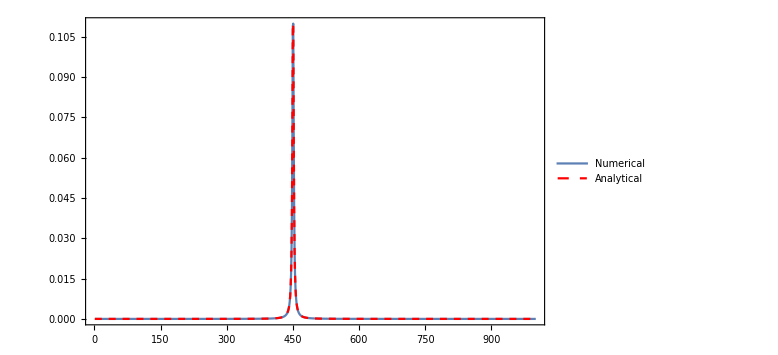

```mathematica
P1=10000/1000;
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLegends-> {"Numerical"},Frame->True,Axes->False,ImageSize->Large
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends-> {"Analytical"}];
Show[a1,a2]
```

```mathematica
(*Pumping the poluation*)
M11=M10/.{Subscript[σ, 1,1]->0,Subscript[σ, 2,2]->1,Subscript[σ, 3,3]->0,Subscript[σ, 4,4]->0};
(*Organize*)
M12=M11/.{γ12 ->- ξ12-ⅈ δ ,γ13 ->-ξ13+ⅈ Δ1,γ14 ->-ξ14+ⅈ w43 +ⅈ Δ1,γ21 ->-ξ21+ⅈ δ ,γ23  ->-ξ23+ⅈ δ +ⅈ Δ1, γ24 ->-ξ24+ⅈ δ +ⅈ Δ1+ⅈ w43 ,γ31  ->-ξ31-ⅈ Δ1,γ32 ->-ξ32-ⅈ δ -ⅈ Δ1 ,γ34 ->-ξ34+ⅈ w43 , γ41  ->-ξ41-ⅈ Δ1-ⅈ w43,γ42 ->-ξ42-ⅈ w43 -ⅈ δ -ⅈ Δ1,γ43 ->-ξ43-ⅈ w43 };
%//TableForm
```

-1/2 ⅈ Ω31 σ_(1,3)-1/2 ⅈ √(7/2) Ω31 σ_(1,4)+1/2 ⅈ Ω13 σ_(3,1)+1/2 ⅈ √(7/2) Ω13 σ_(4,1)==0
-ⅈ δ σ_(1,2)-(-ⅈ δ-ξ12) σ_(1,2)-1/2 ⅈ Ω32 σ_(1,3)-(ⅈ Ω32 σ_(1,4))/(√5)+1/2 ⅈ Ω13 σ_(3,2)+1/2 ⅈ √(7/2) Ω13 σ_(4,2)==0
-1/2 ⅈ Ω23 σ_(1,2)+ⅈ Δ1 σ_(1,3)-(ⅈ Δ1-ξ13) σ_(1,3)+1/2 ⅈ √(7/2) Ω13 σ_(4,3)==0
-(ⅈ Ω23 σ_(1,2))/(√5)+ⅈ w43 σ_(1,4)+ⅈ Δ1 σ_(1,4)-(ⅈ w43+ⅈ Δ1-ξ14) σ_(1,4)+1/2 ⅈ Ω13 σ_(3,4)==0
ⅈ δ σ_(2,1)-(ⅈ δ-ξ21) σ_(2,1)-1/2 ⅈ Ω31 σ_(2,3)-1/2 ⅈ √(7/2) Ω31 σ_(2,4)+1/2 ⅈ Ω23 σ_(3,1)+(ⅈ Ω23 σ_(4,1))/(√5)==0
-1/2 ⅈ Ω32 σ_(2,3)-(ⅈ Ω32 σ_(2,4))/(√5)+1/2 ⅈ Ω23 σ_(3,2)+(ⅈ Ω23 σ_(4,2))/(√5)==0
-(ⅈ Ω23)/2-1/2 ⅈ Ω13 σ_(2,1)+ⅈ δ σ_(2,3)+ⅈ Δ1 σ_(2,3)-(ⅈ δ+ⅈ Δ1-ξ23) σ_(2,3)+(ⅈ Ω23 σ_(4,3))/(√5)==0
-(ⅈ Ω23)/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(2,1)+ⅈ w43 σ_(2,4)+ⅈ δ σ_(2,4)+ⅈ Δ1 σ_(2,4)-(ⅈ w43+ⅈ δ+ⅈ Δ1-ξ24) σ_(2,4)+1/2 ⅈ Ω23 σ_(3,4)==0
1/2 ⅈ Ω32 σ_(2,1)-ⅈ Δ1 σ_(3,1)-(-ⅈ Δ1-ξ31) σ_(3,1)-1/2 ⅈ √(7/2) Ω31 σ_(3,4)==0
(ⅈ Ω32)/2+1/2 ⅈ Ω31 σ_(1,2)-ⅈ δ σ_(3,2)-ⅈ Δ1 σ_(3,2)-(-ⅈ δ-ⅈ Δ1-ξ32) σ_(3,2)-(ⅈ Ω32 σ_(3,4))/(√5)==0
1/2 ⅈ Ω31 σ_(1,3)+1/2 ⅈ Ω32 σ_(2,3)-1/2 ⅈ Ω13 σ_(3,1)-1/2 ⅈ Ω23 σ_(3,2)==0
1/2 ⅈ Ω31 σ_(1,4)+1/2 ⅈ Ω32 σ_(2,4)-1/2 ⅈ √(7/2) Ω13 σ_(3,1)-(ⅈ Ω23 σ_(3,2))/(√5)+ⅈ w43 σ_(3,4)-(ⅈ w43-ξ34) σ_(3,4)==0
(ⅈ Ω32 σ_(2,1))/(√5)-ⅈ w43 σ_(4,1)-ⅈ Δ1 σ_(4,1)-(-ⅈ w43-ⅈ Δ1-ξ41) σ_(4,1)-1/2 ⅈ Ω31 σ_(4,3)==0
(ⅈ Ω32)/(√5)+1/2 ⅈ √(7/2) Ω31 σ_(1,2)-ⅈ w43 σ_(4,2)-ⅈ δ σ_(4,2)-ⅈ Δ1 σ_(4,2)-(-ⅈ w43-ⅈ δ-ⅈ Δ1-ξ42) σ_(4,2)-1/2 ⅈ Ω32 σ_(4,3)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,3)+(ⅈ Ω32 σ_(2,3))/(√5)-1/2 ⅈ Ω13 σ_(4,1)-1/2 ⅈ Ω23 σ_(4,2)-ⅈ w43 σ_(4,3)-(-ⅈ w43-ξ43) σ_(4,3)==0
1/2 ⅈ √(7/2) Ω31 σ_(1,4)+(ⅈ Ω32 σ_(2,4))/(√5)-1/2 ⅈ √(7/2) Ω13 σ_(4,1)-(ⅈ Ω23 σ_(4,2))/(√5)==0

```mathematica
M13=M11[[{2,3,4,5,7,8,9,10,12,13,14,15}]];
(*Only for the first order of the prob*)
f={};
list1={Subscript[σ, 1,2],Subscript[σ, 1,3],Subscript[σ, 1,4],Subscript[σ, 2,1],Subscript[σ, 2,3],Subscript[σ, 2,4],Subscript[σ, 3,1],Subscript[σ, 3,2],Subscript[σ, 3,4],Subscript[σ, 4,1],Subscript[σ, 4,2],Subscript[σ, 4,3]};
pat0=Times[_.,Ω32|Power[Ω32,_],Ω23|Power[Ω23,_]];
ser[expr_]:=DeleteCases[ExpandAll[expr],pat0,Infinity]
(*ser[expr_]:=PolynomialMod[expr,ΩP ΩPc]*)
Do[
Do[
list=list1;
ans=Solve[M13[[q]],list1[[k]]]//Simplify;
If[ans=={},list=Delete[list,k];,Break[];];
,{k,1,12}];
f=Append[f,ans[[1]]];
M13=ser[M13/.ans[[1]]]//Simplify;
Print[q];
,{q,1,12}]
```

1

2

3

4

5

6

7

8

9

10

11

12

```mathematica
Clear[ans]
(*Substitute the solutions, and find the coherent term of the density matrix*)
ans[1]=f[[12]];
Do[
ans[i]=ser[(f[[13-i]]/.Flatten[ans[#]&/@Table[j-1,{j,2,i}]])]//Simplify
,{i,2,12}]
sol=Table[ans[i],{i,1,12}][[All,1]]/.{Ω13 Ω31->omegac1^2,Δ1->Δ,γ23->γ32,γ12->γ21,γ34->γ43,γ24->γ42};
sol/.{Ω13 Ω31->omegac1^2,Δ1->Δ,γ23->γ32,γ12->γ21,γ34->γ43,γ24->γ42}//TableForm
```

σ_(4,3)→0
σ_(4,2)→((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))
σ_(4,1)→0
σ_(3,4)→0
σ_(3,2)→((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))
σ_(3,1)→0
σ_(2,4)→((16 √5 γ32 δ+16 √5 γ21 (ⅈ γ32+δ+Δ)-ⅈ (-4 √5 omegac1^2+5 √14 omegac1^2+16 √5 δ^2+16 √5 δ Δ)) Ω23)/(10 (-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (-omegac1^2+4 δ^2+4 δ Δ))))
σ_(2,3)→((35 ⅈ √2 omegac1^2-4 ⅈ √35 omegac1^2+40 √2 w43 (γ21-ⅈ δ)+40 √2 γ42 δ-40 ⅈ √2 δ^2-40 ⅈ √2 δ Δ+40 √2 γ21 (ⅈ γ42+δ+Δ)) Ω23)/(10 √2 (-7 omegac1^2 γ32-2 omegac1^2 γ42+9 ⅈ omegac1^2 δ+8 ⅈ γ32 γ42 δ+8 γ32 δ^2+8 γ42 δ^2-8 ⅈ δ^3+9 ⅈ omegac1^2 Δ+8 γ32 δ Δ+8 γ42 δ Δ-16 ⅈ δ^2 Δ-8 ⅈ δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (ⅈ γ42+δ+Δ)+w43 (8 γ32 δ+8 γ21 (ⅈ γ32+δ+Δ)-2 ⅈ (-omegac1^2+4 δ^2+4 δ Δ))))
σ_(2,1)→-(2 (5 w43+ⅈ √70 γ32+5 ⅈ γ42+5 δ+√70 δ+5 Δ+√70 Δ) Ω23 Ω31)/(5 (7 ⅈ omegac1^2 γ32+2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ-8 ⅈ γ32 δ^2-8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ-8 ⅈ γ32 δ Δ-8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (ⅈ γ32+δ+Δ) (γ42-ⅈ (δ+Δ))+2 w43 (omegac1^2-4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32-ⅈ (δ+Δ)))))
σ_(1,4)→0
σ_(1,3)→0
σ_(1,2)→-(2 (5 w43-ⅈ √70 γ32-5 ⅈ γ42+5 δ+√70 δ+5 Δ+√70 Δ) Ω13 Ω32)/(5 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))

# Test

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
g1={};
Do[
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω23=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P2/(Pi*(diam2/2)^2)]);Ω32=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P2/(Pi*(diam2/2)^2)]);
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLabel->"P_Coup= "<>ToString[1000P1]<>"mW P_Prob = "<>ToString[1000P2]<>"mW",Frame->True,Axes->False,ImageSize->Small
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed}];
g1=Append[g1,Show[a1,a2]];
,{P1,0,0.05,0.0025},{P2,0.1/1000,1/1000,0.1/1000}]
```

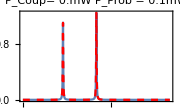
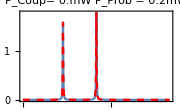
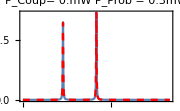
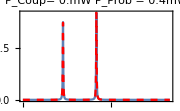
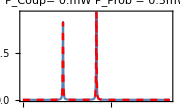
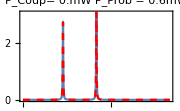
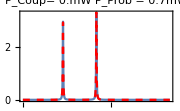
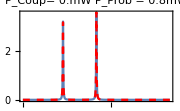
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[g1,10]//TableForm
```

```mathematica
g2={};
Do[
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω23=x Ω13 ;Ω32=x Ω31;
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotLabel->"P_(Coup\)= "<>ToString[1000P1]<>"mW Ratio= "<>ToString[x],Frame->True,Axes->False,ImageSize->Small
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-5*10^9,5*10^9,0.01*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed}];
g2=Append[g2,Show[a1,a2]];
,{P1,{0.0001,0.001,0.01,0.1 ,1,10,100,1000}},{x,{0.0001,0.001,0.01,0.1,1,10,100,1000}}]
Partition[g2,8]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## w43=2*Pi*15.750056 10^6/2

```mathematica
w43=2*Pi*15.750056 10^6/2;
g3={};
Do[
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω23=x Ω13 ;Ω32=x Ω31;
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-.5*10^9,.5*10^9,0.02*10^9}],Joined->True,PlotRange->All,PlotLabel->"P_Coup= "<>ToString[1000P1]<>"mW Ratio= "<>ToString[x],Frame->True,Axes->False,ImageSize->Small
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
δ=0;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-.5*10^9,.5*10^9,0.02*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed}];
g3=Append[g3,Show[a1,a2]];
,{P1,{0.00001,0.0001,0.001,0.01,0.1 ,1,10,100,1000}},{x,{0.00001,0.0001,0.001,0.01,0.1,1,10,100}}]
Partition[g3,8]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## w43=2*Pi*15.750056 10^6/2 scan

```mathematica
w43=2*Pi*15.750056 10^6/2;
g3={};
δ=-Δ;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;

Do[
Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω23=x Ω13 ;Ω32=x Ω31;
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->i,δ->-i},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{i,-.5*10^9,.5*10^9,0.02*10^9}],Joined->True,PlotRange->All,PlotLabel->"P_Coup= "<>ToString[1000P1]<>"mW Ratio= "<>ToString[x],Frame->True,Axes->False,ImageSize->Small
];
omegac1=1Ω13;

a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))],{Δ,-.5*10^9,.5*10^9,0.02*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed}];
g3=Append[g3,Show[a1,a2]];
,{P1,{0.00001,0.0001,0.001,0.01,0.1 ,1,10,100,1000}},{x,{0.00001,0.0001,0.001,0.01,0.1,1,10,100}}]
Partition[g3,8]//TableForm
```

$Aborted

$Aborted

```mathematica
g3={};
Do[
δ=-Δ;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;

Ω13=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);Ω31=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P1/(Pi*(diam/2)^2)]);
Ω23=x Ω13 ;Ω32=x Ω31;
a1=ListPlot[
Table[Im[Total[Solve[
M9[[{2,3,4,5,7,8,9,10,12,13,14,15},2]]==0/.{Subscript[σ, 1,1][t]->0,Subscript[σ, 2,2][t]->1,Subscript[σ, 3,3][t]->0,Subscript[σ, 4,4][t]->0,Δ1->Δ},{Subscript[σ, 1,2][t],Subscript[σ, 1,3][t],Subscript[σ, 1,4][t],Subscript[σ, 2,1][t],Subscript[σ, 2,3][t],Subscript[σ, 2,4][t],Subscript[σ, 3,1][t],Subscript[σ, 3,2][t],Subscript[σ, 3,4][t],Subscript[σ, 4,1][t],Subscript[σ, 4,2][t],Subscript[σ, 4,3][t]}][[1,{8,11},2]]]]
,{Δ,-5*10^9,5*10^9,0.1*10^9}],Joined->True,PlotRange->All,PlotLabel->"P_Coup= "<>ToString[1000P1]<>"mW Ratio= "<>ToString[x],Frame->True,Axes->False,ImageSize->Small
];
omegac1=1Ω13;
γ21=2Pi 1.4*10^6;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
a2=ListPlot[
Table[
Im[((4 √5 omegac1^2-5 √14 omegac1^2+16 ⅈ √5 γ32 δ-16 √5 δ^2-16 √5 δ Δ+16 √5 γ21 (γ32+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))+((35 omegac1^2-2 √70 omegac1^2+40 ⅈ w43 (γ21+ⅈ δ)+40 ⅈ γ42 δ-40 δ^2-40 δ Δ+40 γ21 (γ42+ⅈ (δ+Δ))) Ω32)/(10 (-7 ⅈ omegac1^2 γ32-2 ⅈ omegac1^2 γ42+9 omegac1^2 δ+8 γ32 γ42 δ+8 ⅈ γ32 δ^2+8 ⅈ γ42 δ^2-8 δ^3+9 omegac1^2 Δ+8 ⅈ γ32 δ Δ+8 ⅈ γ42 δ Δ-16 δ^2 Δ-8 δ Δ^2+8 γ21 (-ⅈ γ32+δ+Δ) (γ42+ⅈ (δ+Δ))+2 w43 (omegac1^2+4 ⅈ γ32 δ-4 δ^2-4 δ Δ+4 γ21 (γ32+ⅈ (δ+Δ)))))]/.δ-> -Δ,{Δ,-5*10^9,5*10^9,0.1*10^9}],Joined->True,PlotRange->All,PlotStyle->{Red,Dashed}];
g3=Append[g3,Show[a1,a2]];
,{P1,{0.00001,0.0001,0.001,0.01,0.1 ,1,10,100,1000}},{x,{0.00001,0.0001,0.001,0.01,0.1,1,10,100}}]
Partition[g3,8]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-